```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Markovian beta Data eta_0"];
DataM004=ReadList["LNData_M_beta_0.04_eta_0_.txt"];
DataM005=ReadList["LNData_M_beta_0.05_eta_0_.txt"];
DataM006=ReadList["LNData_M_beta_0.06_eta_0_.txt"];
DataM007=ReadList["LNData_M_beta_0.07_eta_0_.txt"];
DataM008=ReadList["LNData_M_beta_0.08_eta_0_.txt"];
DataM009=ReadList["LNData_M_beta_0.09_eta_0_.txt"];
DataM010=ReadList["LNData_M_beta_0.1_eta_0_.txt"];
DataM011=ReadList["LNData_M_beta_0.11_eta_0_.txt"];
DataM012=ReadList["LNData_M_beta_0.12_eta_0_.txt"];
DataM=Join[{DataM004,DataM005,DataM006,DataM007,DataM008,DataM009,DataM010,DataM011, DataM012}];
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance"];
DataNM004=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.04_eta_0_Omega_0.txt"];
DataNM005=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.05_eta_0_Omega_0.txt"];
DataNM006=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.06_eta_0_Omega_0.txt"];
DataNM007=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.07_eta_0_Omega_0.txt"];
DataNM008=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.08_eta_0_Omega_0.txt"];
DataNM009=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.09_eta_0_Omega_0.txt"];
DataNM010=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.1_eta_0_Omega_0.txt"];
DataNM011=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.11_eta_0_Omega_0.txt"];
DataNM012=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\LNData_NM_beta_0.12_eta_0_Omega_0.txt"];
DataNM=Join[{DataNM004,DataNM005,DataNM006,DataNM007,DataNM008,DataNM009,DataNM010,DataNM011, DataNM012}];
```

```mathematica
height=400;
width=600;
PlotFormat={Joined->True, PlotRange->{0, 3}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black,20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};

MPlots=ListLinePlot[Table[DataM[[betavalue]][[6]], {betavalue, 1, 9}], PlotStyle->Table[Directive[Darker[Red, inc]], {inc, 0.09, 1, 0.09}], Evaluate[PlotFormat]];

NMPlots=ListLinePlot[Table[DataNM[[betavalue]][[6]][[1;;2001]], {betavalue, 1, 9}], PlotStyle->Table[Directive[Dashed, Darker[Red, inc]], {inc, 0.09, 1, 0.09}], Evaluate[PlotFormat]];

CustomColors=Table[Blend[{ Purple, Red, Magenta},x],{x,0,1,1/8}]

MandNMPlots=Rasterize[Show[ListLinePlot[Table[DataM[[betavalue]][[6]][[1;;2001]], {betavalue, 1, 9}], PlotStyle->Table[Directive[CustomColors[[colorvalue]]], {colorvalue, 1, 9}], Evaluate[PlotFormat]],
ListLinePlot[Table[DataNM[[betavalue]][[6]][[1;;2001]], {betavalue, 1, 9}], PlotStyle->Table[Directive[Dashed, CustomColors[[colorvalue]]], {colorvalue, 1, 9}], Evaluate[PlotFormat]]]]

Row[{MPlots, NMPlots, MandNMPlots}]
```

{RGBColor[0.5, 0, 0.5],RGBColor[0.625, 0, 0.375],RGBColor[0.75, 0, 0.25],RGBColor[0.875, 0, 0.125],RGBColor[1, 0, 0],RGBColor[1, 0, Rational[1, 4]],RGBColor[1, 0, Rational[1, 2]],RGBColor[1, 0, Rational[3, 4]],RGBColor[1, 0, 1]}

-Graphics-

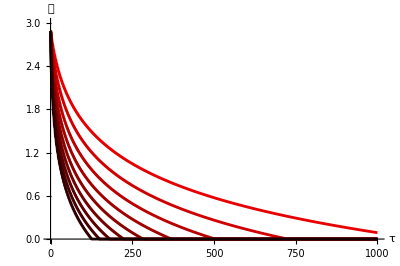
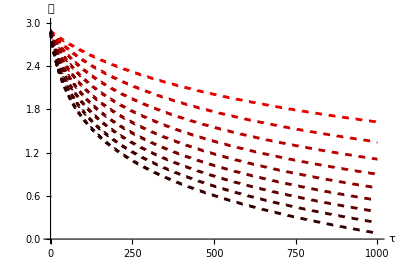
```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Environmental Coupling beta and eta_ 0 no Resonance"];
Export["non-Markovian and Markovian Beta Comparison eta_0.png", MandNMPlots]
```

non-Markovian and Markovian Beta Comparison eta_0.png

```mathematica
DataM004[[6]][[2001]];
DataNM004[[6]][[2001]];
DataNM012[[6]][[2001]];
```

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_0 no resonance\\t_0_1000 beta 2.4 times larger than Markov"];
DataNM012=ReadList["LNData_NM_beta_0.12_eta_0_Omega_0.txt"];
DataNM015=ReadList["LNData_NM_beta_0.15_eta_0_Omega_0.txt"];
DataNM018=ReadList["LNData_NM_beta_0.18_eta_0_Omega_0.txt"];
DataNM021=ReadList["LNData_NM_beta_0.21_eta_0_Omega_0.txt"];
DataNM024=ReadList["LNData_NM_beta_0.24_eta_0_Omega_0.txt"];
DataNM027=ReadList["LNData_NM_beta_0.27_eta_0_Omega_0.txt"];
DataNM030=ReadList["LNData_NM_beta_0.3_eta_0_Omega_0.txt"];
DataNM033=ReadList["LNData_NM_beta_0.33_eta_0_Omega_0.txt"];
DataNM036=ReadList["LNData_NM_beta_0.36_eta_0_Omega_0.txt"];

SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Markovian beta Data eta_0"];
DataM005=ReadList["LNData_M_beta_0.05_eta_0_.txt"];
DataM0625=ReadList["LNData_M_beta_0.0625_eta_0_.txt"];
DataM075=ReadList["LNData_M_beta_0.075_eta_0_.txt"];
DataM0875=ReadList["LNData_M_beta_0.0875_eta_0_.txt"];
DataM010=ReadList["LNData_M_beta_0.1_eta_0_.txt"];
DataM01125=ReadList["LNData_M_beta_0.1125_eta_0_.txt"];
DataM0125=ReadList["LNData_M_beta_0.125_eta_0_.txt"];
DataM01375=ReadList["LNData_M_beta_0.1375_eta_0_.txt"];
DataM015=ReadList["LNData_M_beta_0.15_eta_0_.txt"];
```

{0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36}

{0.05,0.0625,0.075,0.0875,0.1,0.1125,0.125,0.1375,0.15}

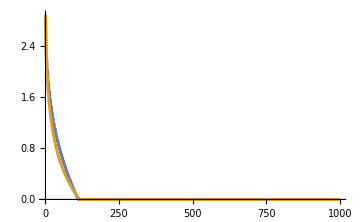

```mathematica
(* Checking if NM > M with βNM = 2.4βM *)
Table[value, {value, 0.12, 0.36, 0.03}]
Table[value/2.4, {value, 0.12, 0.36, 0.03}]
ListLinePlot[{DataNM030[[6]], DataM0125[[6]]}, ImageSize->Medium]
```

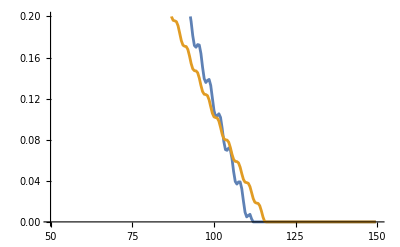

```mathematica
ListLinePlot[{DataNM030[[6]][[50*2;;150*2]], DataM0125[[6]][[50*2;;150*2]]}, PlotRange->{{50, 150}, {0, 0.20}}]
```

```mathematica
DataNM030[[6]][[105*2]][[2]]
DataM0125[[6]][[105*2]][[2]]
```

0.0719751

0.0775966